```mathematica
<<xlr8r.m;
<<Cellzilla2D.m
```

xCellerator 0.95 (28-Feb-2014) loaded Thu 8 Jun 2017 20:05:02
using Mathematica 11.1.1 for Mac OS X x86 (64-bit) (April 27, 2017) (Version 11.1, Release 1)

Cellzilla2D (3.0.51c (08 June 2017)) loaded Thu 8 Jun 2017 20:05:02
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

## Generate a tissue on an approximately square template

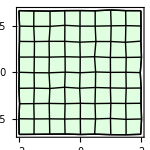

```mathematica
q=RandomizeTemplate[TemplateRectangular[{-2,2,.5},{-2, 2, .5}],.05];
Q=Tissue2DTissue[q];
ShowTissue[Q, Frame-> True]
```

## Demonstrate Growth without any reactions

```mathematica
network={};
diff={};
pumps={};
parameters={k->10,μ->.1,p->1.0, kk-> 0};
```

## Run a simulation

```mathematica
SIM=grow[Q,0,25,
"Internal"-> True, 
"Show"-> False, 
"Reactions"-> network, 
"Pumps"-> pumps,
"Diffusion"-> diff, 
"WallReactions"->{},
"BoundaryConditions"-> {}, 
"EdgeVariable"-> ell,
"CellVariable"-> area,
"Growing"-> True,
"Restlength"-> resting,
"k"-> k,
"mu"-> μ, 
"P"-> p, 
"Parameters"-> parameters, 
"DivisionThreshold"-> 1000, 
"DivisionSigma"-> 0.15, 
"DivisionVariable"-> area
];
```

64 Cells.

0 internal reactions in each cell.

0 total intracellular reactions.

0 transport reactions.

434 algebraic equations for spring growth.

370 total reactions.

Simulation Completed at t = 25. after 0 cell divisions; Normal Exit. CPU: 11.333

## Extract some images at fixed time steps 0, 5, 10, 15, 20, 25

```mathematica
images=Show[GeometricSnapShot[Q, SIM, {x,y},{t, #}], PlotRange-> {{-3, 3}, {-3,3}}, PlotLabel-> "t="<>ToString[#], Frame-> True]&/@Range[0,25,5];
```

## Make a movie using ListAnimate

```mathematica
ListAnimate[images]
```